```mathematica
vr = {r1[t]->OverVector[r1][t],r2[t]->OverVector[r2][t],r[t]->OverVector[r][t],rc[t]->OverVector[rc][t]}
s1=Collect[Solve[
{
r[t]==r1[t]-r2[t],
m1(r1[t]-rc[t])+m2(r2[t]-rc[t])==0
},
{r1[t],r2[t]}
], {r[t],rc[t]}]/.vr
```

{r1[t]→OverVector[r1][t],r2[t]→OverVector[r2][t],r[t]→r⃗[t],rc[t]→OverVector[rc][t]}

{{OverVector[r1][t]→(m2 r⃗[t])/(m1+m2)-((-m1-m2) OverVector[rc][t])/(m1+m2),OverVector[r2][t]→-(m1 r⃗[t])/(m1+m2)-((-m1-m2) OverVector[rc][t])/(m1+m2)}}

```mathematica
s2=Eliminate[{
F1==-F2,
F1==m1 D[r1[t]/.vr/.s1[[1,1]],{t,2}],
F2==m2 D[r2[t]/.vr/.s1[[1,2]],{t,2}]
},{F1,F2}]/.vr
```

OverVector[rc]''[t]==0&&m1+m2≠0

```mathematica
Manipulate[
Module[{sol},
sol =Quiet@ NDSolve[
{(M1 (-a[[1]]+x[t]))/(((-a[[1]]+x[t])^2+(-a[[2]]+y[t])^2)^(3/2))+(M2 (-b[[1]]+x[t]))/(((-b[[1]]+x[t])^2+(-b[[2]]+y[t])^2)^(3/2))+(x^(,,))[t]==0,
(M1 (-a[[2]]+y[t]))/(((-a[[1]]+x[t])^2+(-a[[2]]+y[t])^2)^(3/2))+(M2 (-b[[2]]+y[t]))/(((-b[[1]]+x[t])^2+(-b[[2]]+y[t])^2)^(3/2))+ (y^(,,))[t]==0,
x[0]==0,y[0]==0,x'[0]==vx0,y'[0]==vy0},
{x[t],y[t]},{t,0,tmax}
];
Show[
ParametricPlot[
Evaluate[{x[t],y[t]}/.sol],{t,0,tmax}
],
Graphics[
{Disk[{a[[1]],a[[2]]},0.05 M1],
Disk[{b[[1]],b[[2]]},0.05 M2]}
],ImageSize->{400,400}
]],
Style["initial velocity",Bold],
{{vx0,-1,"x"},-1,1,.01,Appearance->"Labeled",ImageSize->Tiny},
{{vy0,-1,"y"},-1,1,.01,Appearance->"Labeled",ImageSize->Tiny},
Style["mass",Bold],
{{M1,1,"planet 1"},.5,2,.01,Appearance->"Labeled",ImageSize->Tiny},
{{M2,1,"planet 2"},.5,2,.01,Appearance->"Labeled",ImageSize->Tiny},
Style["location",Bold],
{{a,{-1,0},"planet 1"},{-1.5,-.5},{-.5,.5},ImageSize->Tiny},
{{b,{1,0},"planet 2"},{.5,-.5},{1.5,.5},ImageSize->Tiny},
Delimiter,
{{tmax,10,"time"},1,100,.01,Appearance->"Labeled",ImageSize->Tiny},
ControlPlacement->Left,
SynchronousUpdating->False
]
```

```mathematica
Manipulate[
Module[
{},
G=QuantityMagnitude[UnitConvert[Quantity["GravitationalConstant"]]];
m1= QuantityMagnitude[UnitConvert[Quantity["EarthMass"]]];
m2 = QuantityMagnitude[PlanetaryMoonData["Moon","Mass"]];
μ=G (m1+m2);
PolarPlot[h^2/μ/(1+e Cos[θ]),{θ,0,2 Pi}]
],{}
]
```

Manipulate::vsform: Manipulate argument {} does not have the correct form for a variable specification.

Manipulate[Module[{},G=QuantityMagnitude[UnitConvert[Quantity[GravitationalConstant]]];m1=QuantityMagnitude[UnitConvert[Quantity[EarthMass]]];m2=QuantityMagnitude[PlanetaryMoonData[Moon,Mass]];μ=G (m1+m2);PolarPlot[h^2/(μ (1+e Cos[θ])),{θ,0,2 π}]],{}]

7.346×10^22

```mathematica
Module[
{},
G=QuantityMagnitude[UnitConvert[Quantity["GravitationalConstant"]]];
m1= QuantityMagnitude[UnitConvert[Quantity["EarthMass"]]];
m2 = QuantityMagnitude[PlanetaryMoonData["Moon","Mass"]];
μ=G (m1+m2);
PolarPlot[h^2/μ/(1+e Cos[θ]),{θ,0,2 Pi}]
]
```

-Graphics-

```mathematica
path="/home/ysl/Code/mynotes/principia/img/"
```

/home/ysl/Code/mynotes/principia/img/

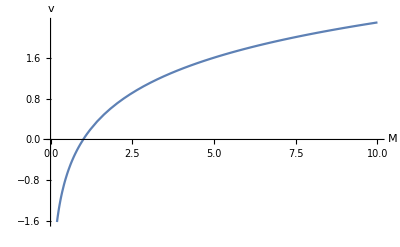

```mathematica
tsiolkovsky=Plot[{Log[M]},{M,0,10},AxesLabel->{"M","v"}]
```

```mathematica
Export[path<>"tsiolkovsky.jpg",tsiolkovsky]
```

/home/ysl/Code/mynotes/principia/img/tsiolkovsky.jpg

```mathematica
Clear[v];Simplify[(M-dM)(v+dv)+dM(v+dv-w) == M v]  (*Tsiolkovsky differential equation by momentum conservation*)
```

dv M==dM w

```mathematica
DSolve[v[t]==w/M[t] M'[t],M[t],t]


Manipulate[
Module[{EV,sol,Rneed,Rgive,parameters,equationplot,functionplot,rocketplot,r,h,earth},
(* solve equation and use result *)
EV=If[level=="first",firstEV,If[level=="second",secondEV,thirdEV]];
sol=FindRoot[EV==ve* Log[E,Rneed],{Rneed,1}];
Rneed=sol[[1]][[2]];
Rgive=N[M0/MF];

(* load rocket dynamic parameters *)
parameters=rocketdynamics[time,ve,M0,MF,m];

(* rocket equation plot *)
equationplot=Plot[Tooltip[ve Log[E,MR],"rocket equation"],{MR,1,50},
PlotLabel->Row[{"rocket equation ", Style["V",Italic]," = ",Style[Subscript["v","e"],Italic]," lnM_0/M"}],
FrameLabel->{Row[{"mass ratio ",Style["R",Italic]," = ",Subscript[Style["M",Italic],0],"/",Style["M",Italic]}],Row[{"velocity ",Style["V",Italic], "(m/s)"}]},
PlotStyle->Directive[Blue,Thick],PlotRange->{{1,50},{0,21000}},AxesOrigin->{0.1,0},Frame->True,
ImageSize-> imagesize,ImagePadding->imagepadding,
Epilog->{Thick,Dotted,Orange,PointSize[Large],
Tooltip[Line[{{1,EV},{Rneed,EV}}],Row[{level," escape velocity = ",EV,"m/s"}]],
Tooltip[Line[{{Rneed,0},{Rneed,EV}}],Row[{"required mass ratio = ",NumberForm[Rneed,{3,2}]}]],
Tooltip[Point[{Rneed,EV}],"cross point"],
Dashed,Black,
Tooltip[Line[{{Rgive,0},{Rgive,21000}}],Row[{"designed mass ratio = ",NumberForm[Rgive,{3,2}]}]],
Blue,
Tooltip[Point[{parameters[[4]],parameters[[6]]}],Row[{"velocity = ",parameters[[6]]}]]}];

(* rocket dynamic function and plot *)
functionplot=Plot[{
Tooltip[(1/scale)*acceleration[t,ve,M0,m],"acceleration curve"],
Tooltip[velocity[t,ve,M0,m],"velocity curve"],
Tooltip[scale*altitude[t,ve,M0,m],"altitude curve"]
},{t,0,parameters[[2]]},
PlotRange->{{0,parameters[[2]]+100},{0,2.1*10^4}},
PlotStyle->{Directive[Red,Thick],Directive[Blue,Thick],Directive[Green,Thick]},
PlotLabel->Row[{"dynamic parameters"}],ImageSize-> imagesize,ImagePadding->imagepadding,
Frame->True,
FrameLabel->{"flight time t (s)",Column[{
Row[{"acceleration ",Style["a",Italic]," (",Style["m",Italic],"/",Style["s",Italic],") x 10^-2"}],Row[{"velocity ",Style["V",Italic]," (",Style["m",Italic],"/",Style["s",Italic],")"}],
Row[{"altitude ",Style["S",Italic]," (",Style["m",Italic],")x 10^2"}]
}]},
Epilog->{
Thick,Dotted,PointSize[Large],Red,
Tooltip[Line[{{0,(1/scale)*uplimits},{parameters[[2]]+100,(1/scale)*uplimits}}],Row[{"acceleration limits ",uplimits,"(m/s^2)"}]],
Dashed,Black,
Tooltip[Line[{{parameters[[2]],0},{parameters[[2]],2.1*10^4}}],Row[{"burn out at ",NumberForm[parameters[[2]],{5,1}],"(s)"}]],
Red,
Tooltip[Point[{parameters[[1]],(1/scale)*parameters[[5]]}],Row[{"acceleration = ",parameters[[5]],"(m/s^2)"}]],
Blue,
Tooltip[Point[{parameters[[1]],parameters[[6]]}],Row[{"velocity = ",parameters[[6]],"(m/s)"}]],
Green,
Tooltip[Point[{parameters[[1]],scale*parameters[[7]]}],Row[{"altitude = ",0.001*parameters[[7]],"(km)"}]]
}
];

(* plot rocket 3D model *)
rocketplot=rocketmodel[scale*parameters[[7]],conehght,bodyhght,bodyradius,If[view=="front",Front,{10,10,10}]];

(* show earth *)
r=6378.7; (* earth radius, unit:km *)
h=0.001*parameters[[7]]; (* rocket altitude, unit:km *)
earth=Graphics3D[{Opacity[.5],Tooltip[Sphere[{0,0,0}, r],Row[{"earth radius = ",r,"(km)"}]],
PointSize[Large],Opacity[1],Red,Tooltip[Point[{0,0,r+h}],Row[{"rocket altitude = ",h,"(km)"}]],
Yellow,Tooltip[Point[{0,0,r}],"launch site"]},
Boxed->False,SphericalRegion->True,Background->Black,ImageSize->{340,400}];

If[option=="ground",Grid[{{Column[{equationplot,functionplot}],rocketplot}}],earth]],
Style["target escape velocity",Bold],
{{level,"first","level"},{"first","second","third"},ControlType -> Setter,ImageSize->Tiny},
Delimiter,
Style["geometry",Bold],
{{conehght,5,"head height h_1"},3,10,0.1,Appearance->"Labeled",ImageSize->Tiny},
{{bodyhght,20,"body height h_2"},5,30,1,Appearance->"Labeled",ImageSize->Tiny},
{{bodyradius,1,"body radius r_2"},1,3,0.1,Appearance->"Labeled",ImageSize->Tiny},
Delimiter,
Style["specification",Bold],
{{M0,500,"initial mass M_0"},100,1000,1,Appearance->"Labeled",ImageSize->Tiny},
{{MF,60,"final mass M_F"},10,90,1,Appearance->"Labeled",ImageSize->Tiny},
Delimiter,
Style["performance",Bold],
{{ve,4500,"exhaust velocity v_e"},1000,5000,100,Appearance->"Labeled",ImageSize->Tiny},
{{m,2,"mass flow rate m"},1,20,1,Appearance->"Labeled",ImageSize->Tiny},
{{uplimits,180,"acceleration limits a_l"},150,200,1,Appearance->"Labeled",ImageSize->Tiny},
Delimiter,
Style["launch",Bold],
{{view,"front","view point"},{"front","side"},ControlType ->Setter,ImageSize->Tiny},
{{option,"ground","view option"},{"ground","earth"},ControlType ->Setter,ImageSize->Tiny},
{{showtime,200,"time maximum t_max"},{100,200,500,1000},ControlType ->Setter,ImageSize->Tiny},
{{time,0,"flight time t"},0,showtime,1,ImageSize->Tiny,ControlType->Trigger},
ControlPlacement->Left,
TrackedSymbols->True,
SynchronousUpdating->False,
SynchronousInitialization->False,
AutorunSequencing->{2,3,4,13},
Initialization:>{
(* resize image *)
imagesize={230,200};
imagepadding={{80,5},{35,30}};
scale=0.01;

(* escape velocity data *)
firstEV=7.83*10^3;   
secondEV=11.2*10^3;
thirdEV=16.6*10^3;

(* rocket launch physical model *)
(* current rocket mass *)
mass[t_,M0_,m_]:=M0-m*t;
(* current rocket mass ratio *)
massratio[t_,M0_,m_]:=N[M0/mass[t,M0,m]];
(* rocket acceleration *)
acceleration[t_,ve_,M0_,m_]:=N[(m ve)/(M0-m t)];
(* rocket velocity *)
velocity[t_,ve_,M0_,m_]:=N[ve*Log[E,M0/mass[t,M0,m]]];
(* rocket altitude *)
altitude[t_,ve_,M0_,m_]:=N[ve*M0/m(1-mass[t,M0,m]/M0(Log[E,M0/mass[t,M0,m]]+1))];
(* rocket dynamics parameters *)
rocketdynamics[t_,ve_,M0_,M_,m_]:=
Module[{burntime},
(* rocket burn out time / Max flight time *)
burntime=N[M0/m*(1-M/M0)];
If[t<= burntime,
{t,burntime,mass[t,M0,m],massratio[t,M0,m],
acceleration[t,ve,M0,m],velocity[t,ve,M0,m],altitude[t,ve,M0,m]},
{burntime,burntime,mass[burntime,M0,m],massratio[burntime,M0,m],
acceleration[burntime,ve,M0,m],velocity[burntime,ve,M0,m],altitude[burntime,ve,M0,m]}]
];

(* graphics 3D rocket model *)
rocketmodel[position_,height1_,height2_,radius_,view_]:=
Module[{cone,head,headplus,body,wings,nozzle,ground},
cone[p_,r_,ϕ_,θ_,h1_]:=p+{r*Cos[ϕ]θ/Pi,r*Sin[ϕ]θ/Pi,(1-θ/Pi)h1};
head[p_,r_,h1_]:=ParametricPlot3D[{cone[{0,0,p},r,ϕ,θ,h1]},{ϕ,0,2π},{θ,0,π},Boxed->True,Mesh->None,Axes->True];
headplus[p_,r_,h1_]:=Graphics3D[{Cylinder[{{0,0,p},{0,0,1.5*h1+p}},0.1*r]}];
body[p_,r_,h2_]:=Graphics3D[{Cylinder[{{0,0,p},{0,0,-h2+p}},r]},BaseStyle->{Opacity[1],EdgeForm[]},Lighting->Automatic, Boxed->False,Axes->False,Background->LightBlue, ImageSize->{110,400},ViewPoint->view];
wings[p_,r_,h2_]:=Graphics3D[{
Polygon[{{0,0,-0.5h2+p},{0,2r,-0.7h2+p},{0,2r,-h2+p},{0,0,-0.8h2+p}}],
Polygon[{{0,0,-0.5h2+p},{0,-2r,-0.7h2+p},{0,-2r,-h2+p},{0,0,-0.8h2+p}}],
Polygon[{{0,0,-0.5h2+p},{2r,0,-0.7h2+p},{2r,0,-h2+p},{0,0,-0.8h2+p}}],
Polygon[{{0,0,-0.5h2+p},{-2r,0,-0.7h2+p},{-2r,0,-h2+p},{0,0,-0.8h2+p}}]
}];
quadraticsurface[p_,r_,t_]:=p+{r Cos[t],r Sin[t],-r^2};
nozzle[p_,r_,h2_]:=ParametricPlot3D[quadraticsurface[{0,0,-h2+0.2r+p},rad,t],{t,0,2Pi},{rad,0,1},Mesh->None];
ground[p_,r_,h2_]:=Graphics3D[{Green,Opacity[.5],Polygon[{{-10r,-10r,-(h2+1)},{-10r,10r,-(h2+1)},{10r,10r,-(h2+1)},{10r,-10r,-(h2+1)}}]}];
Show[body[position,radius,height2],head[position,radius,height1],headplus[position,radius,height1],nozzle[position,radius,height2],ground[position,radius,height2],wings[position,radius,height2]]
];
}]
```